Carbapenem Resistance

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

#### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="United States"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years];
nop = (Length[data]-4)/2;
isolates = data[[2;;Length[data]-3;;2]];
resistance = data[[3;;Length[data]-3;;2]];
rfreq =resistance/isolates;
carbcons = data[[-3]]/40;
conbreak = data[[-2,1;;nop]];
cardiv =Table[carbcons*conbreak[[i]],{i,1,nop}];
pc =  data[[-1,1]]; (*proportion of carbapanem prescription out of all antibiotics prescribed for bacterial pneuomonia NOTE: Update with better estimate.*)
tc = cardiv/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
prop = cardiv/tc;
diff = tc-cardiv;
```

```mathematica
cardiv
```

{{0.208775,0.246056,0.29825,0.305706,0.328075,0.3579,0.395181,0.410094,0.439919,0.462288,0.469744,0.492113,0.499569},{0.319298,0.376316,0.45614,0.467544,0.501754,0.547368,0.604386,0.627193,0.672807,0.707017,0.718421,0.752631,0.764035},{0.122808,0.144738,0.17544,0.179826,0.192984,0.210528,0.232458,0.24123,0.258774,0.271932,0.276318,0.289476,0.293862}}

#### Model

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.
The functional form of the model is LinguisticAssistant

```mathematica
r[t_,r0_,b_] := ⅇ^(Total[cn[[1;;t]]]+b*t)/((1/r0)-1+ⅇ^( Total[cn[[1;;t]]]+b*t)) ; (*dA/dt= Subscript[R, C] CA + Subscript[R, N] A, dB/dt= Subscript[N, C] CB + Subscript[N, N] B=> m = a ∑_(i=1)^t Subscript[p, t] Subscript[C, t] + bt and  a = Subscript[R, C]-Subscript[N, C], b=Subscript[R, N]-Subscript[N, N]*)
```

```mathematica
LinguisticAssistant
Maximum Likelihood Function
```

Note: The likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.

```mathematica
Lik[r0_,b_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,b]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,b]],{j,1,tt}]]
```

#### Model Fitting

Using NMaximize function to optimize the likelihood function defined above.

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fb = max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardiv[[i]],df =diff[[i]],{max[[i]],{fr0[[i]],fb[[i]]}}=NMaximize[{Lik[r0,b],0< r0< 1, b<0},{r0,b}, MaxIterations->100000]}]
max
mfr0 = Table[fr0[[i]][[2]],{i,1,3}] 
mfb = Table[fb[[i]][[2]],{i,1,3}]
```

{-158.475,-222.084,-107.343}

{0.00188692,0.223385,0.135864}

{-1.63744×10^-33,-0.528456,-0.0376211}

#### Plots

Putting together observed and fitted data together for plotting.

```mathematica
t=Range[1,tt]; 
res = Table[Transpose@{years,rfreq[[i]]},{i,1,nop}]; (*resistance frequency data*)
x  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardiv[[i]],df =diff[[i]],x[[i]] = Table[r[j,mfr0[[i]],mfb[[i]]],{j,1,tt}]}];
fit =  Table[Transpose@{years,x[[i]]},{i,1,nop}];
```

Show plots

```mathematica
plotD = Table[ListPlot[{res[[i]]},PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}],{i,1,nop}];
plotM = Table[ListLinePlot[{fit[[i]]},PlotStyle->{{Orange,Thick}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Model fit"}],{i,1,nop}];
```

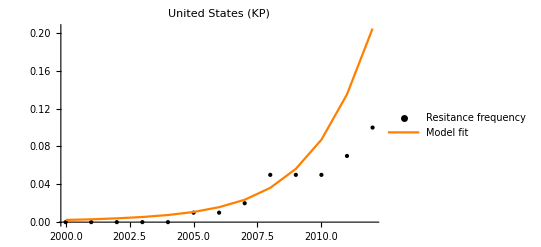

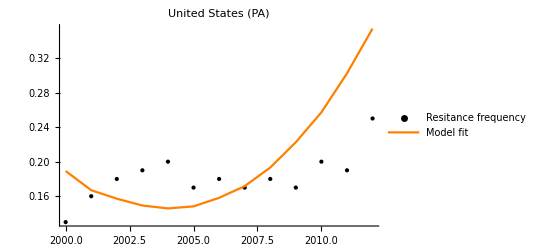

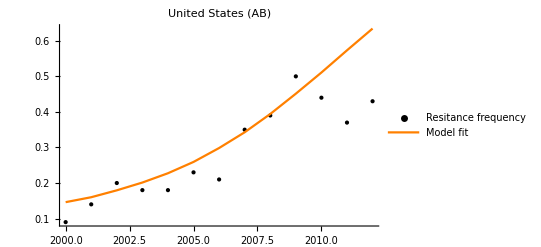

```mathematica
Show[plotD[[1]],plotM[[1]],PlotRange->All,PlotLabel->"United States (KP)"] 
Show[plotD[[2]],plotM[[2]],PlotRange->All,PlotLabel->"United States (PA)"]
Show[plotD[[3]],plotM[[3]],PlotRange->All,PlotLabel->"United States (AB)"]
```

#### Projections

We project the impact of reduction in carbapenem consumption on the antibiotic resistance frequencies in pathogens considered.

```mathematica
curcarb = carbcons[[-1]];  (*current carbapenem consumption*)
py =2020; (*projection till year py*) 
npy = py -years[[-1]];
pyears = Range[ years[[-1]],py];

(*Status Quo consumtions*)
projSQ =ConstantArray[curcarb,Round[npy]];  (*maintaining current carbapenem consumption levels*) 
carbconSQ = Join[carbcons,projSQ];
cardivSQ =Table[carbconSQ*conbreak[[i]],{i,1,nop}];
tcSQ = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffSQ = tcSQ-cardivSQ;
(*Intervention consumtions*)
intv = 0.01; (*reducing current carbapenem consumption by (1-intv) % in next npy years linearly*)
projI = Range[curcarb,intv*curcarb,curcarb*(intv-1)/(npy-1)];
carbconI = Join[carbcons,projI];
cardivI =Table[carbconI*conbreak[[i]],{i,1,nop}];
tcI = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffI = tcI-cardivI;
(*Status Quo resistances*)
y  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardivSQ[[i]],df =diffSQ[[i]],y[[i]] = Table[r[j,mfr0[[i]],mfb[[i]]],{j,tt,tt+npy}]}];
prrSQ =  Table[Transpose@{pyears,y[[i]]},{i,1,nop}];
(*Intervention resistances*)
z  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],cn = cardivI[[i]],df =diffI[[i]],z[[i]] = Table[r[j,mfr0[[i]],mfb[[i]]],{j,tt,tt+npy}]}];
prrI =  Table[Transpose@{pyears,z[[i]]},{i,1,nop}];
y
z
```

{{0.204688,0.297824,0.411417,0.535305,0.654985,0.757789,0.837557,0.894705,0.933348},{0.3541,0.409632,0.467569,0.526393,0.584494,0.640338,0.692622,0.740388,0.783056},{0.634419,0.691568,0.743397,0.789172,0.828663,0.86205,0.889797,0.912528,0.930935}}

{{0.204688,0.297824,0.394421,0.482381,0.554064,0.606843,0.641151,0.658364,0.659487},{0.3541,0.409632,0.440788,0.445592,0.423826,0.376664,0.308224,0.227726,0.149058},{0.634419,0.691568,0.735389,0.767681,0.790314,0.804839,0.812335,0.813382,0.80806}}

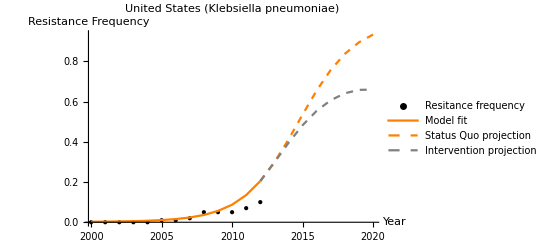

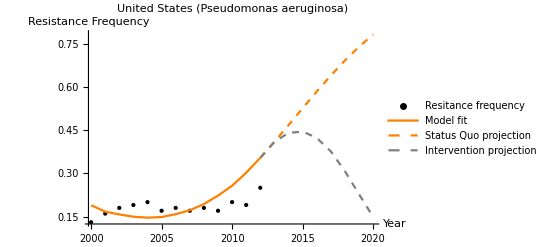

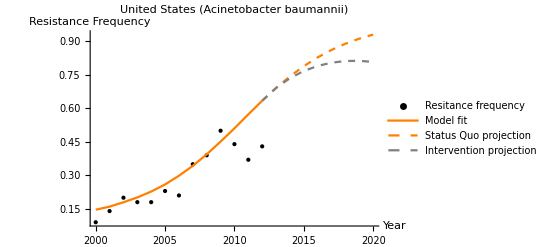

```mathematica
plotPSQ = Table[ListLinePlot[{prrSQ[[i]]},PlotStyle->{{Orange,Thick,Dashed}},PlotStyle->Gray,AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Status Quo projection"}],{i,1,nop}];
plotPI = Table[ListLinePlot[{prrI[[i]]},PlotStyle->{{Gray,Thick,Dashed}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Intervention projection"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],plotPSQ[[1]],plotPI[[1]],PlotRange->All,PlotLabel->"United States (Klebsiella pneumoniae)",AxesLabel->{"Year","Resistance Frequency"}] 
Show[plotD[[2]],plotM[[2]],plotPSQ[[2]],plotPI[[2]],PlotRange->All,PlotLabel->"United States (Pseudomonas aeruginosa)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[3]],plotM[[3]],plotPSQ[[3]],plotPI[[3]],PlotRange->All,PlotLabel->"United States (Acinetobacter baumannii)",AxesLabel->{"Year","Resistance Frequency"}]
```